```mathematica
ClearAll["Global`*"]
```

```mathematica
E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
EM2[n_,a_,b_] := EM2[n,a,b]=Sum[(-1)^k Binomial[k-1,k-a]E2a[n,k,b],{k,1,Log[If[b<2,b,2],n]}];EM2[n_,0,b_]:=1
E1e2[n_,k_,b_]:=Sum[FactorialPower[-k,a]/a! EM2[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
D1g[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j E1e2[n/b^j,k,b],{j,0,Log[b,n]}]
D1h[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j (Sum[FactorialPower[-k,a]/a! EM2[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}]),{j,0,Log[b,n]}]
D1i[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j  FactorialPower[-k,a]/a! EM2[n/b^j,a,b],{j,0,Log[b,n]},{a,0,Log[If[b>2,2,b],n/b^j]}]
D1ia[n_, k_, b_] := Grid[Table[ Binomial[k+j-1,k-1] b^j  FactorialPower[-k,a]/a! EM[n/b^j,a,b],{j,0,Log[b,n]},{a,0,Log[If[b>2,2,b],n/b^j]}]]
D1ib[n_, k_, b_] := Grid[Table[ Binomial[k+j-1,k-1] b^j  FactorialPower[-k,a]/a! EM[n/b^j,a,b]/k,{j,0,Log[b,n]},{a,0,Log[If[b>2,2,b],n/b^j]}]]
D1ic[n_, k_, b_] := Grid[Table[ Binomial[k+j-1,k-1]  FactorialPower[-k,a]/a! ,{j,0,7},{a,0,7}]]
D1id[n_, k2_, b_] := Grid[Table[ Limit[Binomial[k+j-1,k-1]  FactorialPower[-k,a]/a! /k,k->k2],{j,0,7},{a,0,7}]]
```

```mathematica
D1ia[100,1,2]
```

EM[100,0,2] | -EM[100,1,2] | EM[100,2,2] | -EM[100,3,2] | EM[100,4,2] | -EM[100,5,2] | EM[100,6,2]
2 EM[50,0,2] | -2 EM[50,1,2] | 2 EM[50,2,2] | -2 EM[50,3,2] | 2 EM[50,4,2] | -2 EM[50,5,2] | 
4 EM[25,0,2] | -4 EM[25,1,2] | 4 EM[25,2,2] | -4 EM[25,3,2] | 4 EM[25,4,2] |  | 
8 EM[25/2,0,2] | -8 EM[25/2,1,2] | 8 EM[25/2,2,2] | -8 EM[25/2,3,2] |  |  | 
16 EM[25/4,0,2] | -16 EM[25/4,1,2] | 16 EM[25/4,2,2] |  |  |  | 
32 EM[25/8,0,2] | -32 EM[25/8,1,2] |  |  |  |  | 
64 EM[25/16,0,2] |  |  |  |  |  |

```mathematica
D1ia[100,-1,20]
```

EM[100,0,20] | EM[100,1,20] | 0 | 0 | 0 | 0 | 0
-20 EM[5,0,20] | -20 EM[5,1,20] | 0 |  |  |  |

```mathematica
D1ib[100,.000001,2]
```

1.×10^6 EM[100,0,2] | -1. EM[100,1,2] | 0.500001 EM[100,2,2] | -0.333334 EM[100,3,2] | 0.25 EM[100,4,2] | -0.2 EM[100,5,2] | 0.166667 EM[100,6,2]
2. EM[50,0,2] | -2.×10^-6 EM[50,1,2] | 1.×10^-6 EM[50,2,2] | -6.66668×10^-7 EM[50,3,2] | 5.00001×10^-7 EM[50,4,2] | -4.00001×10^-7 EM[50,5,2] | 
2. EM[25,0,2] | -2.×10^-6 EM[25,1,2] | 1.×10^-6 EM[25,2,2] | -6.66668×10^-7 EM[25,3,2] | 5.00001×10^-7 EM[25,4,2] |  | 
2.66667 EM[25/2,0,2] | -2.66667×10^-6 EM[25/2,1,2] | 1.33334×10^-6 EM[25/2,2,2] | -8.88892×10^-7 EM[25/2,3,2] |  |  | 
4.00001 EM[25/4,0,2] | -4.00001×10^-6 EM[25/4,1,2] | 2.00001×10^-6 EM[25/4,2,2] |  |  |  | 
6.40001 EM[25/8,0,2] | -6.40001×10^-6 EM[25/8,1,2] |  |  |  |  | 
10.6667 EM[25/16,0,2] |  |  |  |  |  |

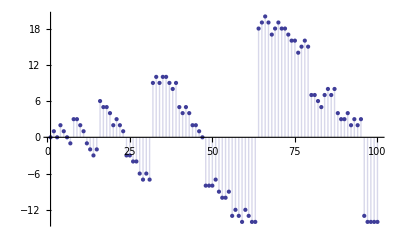

```mathematica
DiscretePlot[ EM2[n,1,2],{n,1,100}]
```

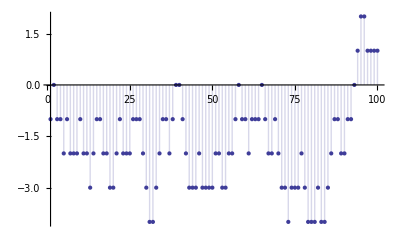

```mathematica
DiscretePlot[ -1+EM2[n,1,2]-2EM2[Floor[n/2],1,2],{n,1,100}]
```

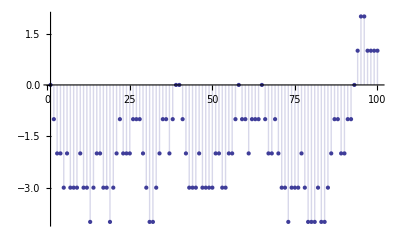

```mathematica
DiscretePlot[If[n>19,-19,0]+ EM2[n,1,20]-20EM2[Floor[n/20],1,20],{n,1,100}]
```

```mathematica
D1ic[100,-2,2]
```

1 | 2 | 1 | 0 | 0 | 0 | 0 | 0
-2 | -4 | -2 | 0 | 0 | 0 | 0 | 0
1 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
D1id[100,0,2]
```

∞ | -1 | 1/2 | -1/3 | 1/4 | -1/5 | 1/6 | -1/7
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
D1i[100,1,1.1]
```

100.357

```mathematica
dra[n_, k_, b_] := DiscretePlot[Sum[ Binomial[k+j-1,k-1] b^j  FactorialPower[-k,a]/a! EM2[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
dra2[n_, k_, b_] := DiscretePlot[{(1/k)Sum[ Binomial[k+j-1,k-1] b^j  FactorialPower[-k,a]/a! EM2[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}]},{j,0,Log[b,n]}]
```

```mathematica
$RecursionLimit=10000
```

10000

```mathematica
dra[3,1,1.01]
```

-Graphics-

```mathematica
Limit[(D1i[100,z,2]-1)/z,z->0]
```

428/15